## Function Definitions and Variable Declarations

### General Tools

```mathematica
aoutColumnName="AOUT";
probeColumnName="PRB";
pumpColumnName="PMP";
referenceColumnName="REF";
wavelengthColumnName="WAV";
modelA4=a1/(δ)^2+a2/(δ)^4+θo;
modelA2=a1/(δ)^2+θo;
modelB4=a1/(δ-b)^2+a2/(δ-b)^4+θo;
modelB2=a1/(δ-b)^2+θo;
getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2)  ;
transGHz={-3.072,-1.372,1.84,4.576};

CalculateBdotL[magVolt1_,magVolt2_]:=Module[{c1x2,c1x1,c1x0,c2x2,c2x1,c2x0,c1v2iSlope,c1v2iInt,c2v2iSlope,c2v2iInt,i1,i2,},
(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1=magVolt1*c1v2iSlope+c1v2iInt;
i2=magVolt2*c2v2iSlope+c2v2iInt;

(*Creates a function for obtaining the magnetic field at a given position based on the currents
in the magnets *)

Integrate[getBEq[i1,i2],{x,0,2.794}] /100/10000(* Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"-> "",":"->""}]->joinedWithSpaces];
,
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"->"",":"->""}]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

QuickPlotRbProfile[dataset_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro,rbAbsorptionPmp},
rbAbsorptionRef=Normal[dataset[All,{"AOUT","REF"}][[All,Values]]];
rbAbsorptionPro=Normal[dataset[All,{"AOUT","PRB"}][[All,Values]]];
rbAbsorptionPmp=Normal[dataset[All,{"AOUT","PMP"}][[All,Values]]];
ListPlot[{rbAbsorptionPro,rbAbsorptionRef,rbAbsorptionPmp},Ticks-> {Range[0,1023,100],Automatic},GridLines->{Range[0,1023,100],None},ImageSize->{Medium,Automatic}]
];

QuickPlotRbProfileWithRange[dataset_,plotRange_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro,rbAbsorptionPmp},
rbAbsorptionRef=Normal[dataset[All,{"AOUT","REF"}][[All,Values]]];
rbAbsorptionPro=Normal[dataset[All,{"AOUT","PRB"}][[All,Values]]];
rbAbsorptionPmp=Normal[dataset[All,{"AOUT","PMP"}][[All,Values]]];
ListPlot[{rbAbsorptionPro,rbAbsorptionRef,rbAbsorptionPmp},PlotRange->{plotRange,Full},Ticks-> {Range[0,1023,20],Automatic},GridLines->{Range[0,1023,20],None},ImageSize->{Full,Automatic}]
];

CompareProfiles[fileName1_,fileName2_]:=
Module[{rawFile,headerStrippedData,columnHeaderLineNumber,j,k,ass,tabularData,ds,profile1,profile2},
profile1=Normal[ConvertAoutProfileToDetuning[GetRbProfileDataset[fileName1],165,"D","A"][All,{"DET","REF"}][[All,Values]]];
profile2=Normal[ConvertAoutProfileToDetuning[GetRbProfileDataset[fileName2],165,"D","A"][All,{"DET","REF"}][[All,Values]]];
ListPlot[{profile1,profile2},PlotRange->{Full,Full},Ticks-> {Range[0,1023,20],Automatic},GridLines->{Range[0,1023,20],None},ImageSize->{Full,Automatic}]
];

RemoveBackgroundFromSaturatedProfile[absorptionDataset_]:=Module[{dataset,noAbsNeg,noAbsPos,wings,linearModelWings,intensitySlope,intensityIntercept,detuning,intensity,x},
{detuning,intensity}=Transpose[absorptionDataset];
intensity=intensity-Min[intensity];
Transpose[{detuning,intensity}
]];

(* Uses the far detunings of the profile, the "wings", to establish the unabsorbed intensity and normalize the profile *)
NormalizeProfile[absorptionDataset_]:=Module[{dataset,noAbsNeg,noAbsPos,wings,linearModelWings,intensitySlope,intensityIntercept,detuning,intensity,x},
dataset=absorptionDataset;
noAbsNeg=dataset[Select[#DET<-4.5&]];(*Selects only data with detunings less than -4.5, where no absorption is present. *)
noAbsNeg=noAbsNeg[All,{"DET","PRB"}];(*Removes all data from dataset except the detunings and the intensity of the probe laser *)
noAbsNeg=Normal[noAbsNeg[[All,Values]]]; (* Removes the headers from the dataset, giving a matrix of the ordered pairs of the data *)

noAbsPos=dataset[Select[#DET>6&]];(*See the above comments*)
noAbsPos=noAbsPos[All,{"DET","PRB"}];
noAbsPos=Normal[noAbsPos[[All,Values]]];

wings=Join[Normal[noAbsNeg,noAbsPos]];
linearModelWings=LinearModelFit[wings,x,x];
intensitySlope=linearModelWings["BestFitParameters"][[2]];
intensityIntercept=linearModelWings["BestFitParameters"][[1]];
detuning=Normal[absorptionDataset[All,"DET"]];
intensity=Normal[absorptionDataset[All,"PRB"]];
intensity=intensity/(intensityIntercept+intensitySlope*detuning);
(*Transpose[{detuning,intensity};*)
absorptionDataset[All,<|#,"PRBNRMWWING"-> #PRB/(intensityIntercept+intensitySlope*#DET)|>&]
];

SlopeInterceptProfileConversion[dataset_,slope_,intercept_]:=
Module[
{},
dataset[All,<|"DET"->#AOUT*slope+intercept,"PRB"->#PRB,"PMP"->#PMP,"REF"->#|>&]
];

ConvertAoutProfileToDetuning[dataset_,firstMinimum_,transitionLetter_,lastTransitionLetter_]:=Module[{CtoDDiff,BtoCDiff,AtoBDiff,aoutSteps,s,startPos,rbAbsorptionRef,scanStepSize,posLower,posUpper,i,j,k,transAout,peak,aoutPos,aoutPrev,aoutStep,aoutNextApprox,aoutConvData,lm,aoutConv,aoutIntercept},
CtoDDiff=115;
BtoCDiff=125;
AtoBDiff=72;

aoutSteps={AtoBDiff,BtoCDiff,CtoDDiff};

(*Find the closest data point to the value chosen by the user*)
s=Nearest[Normal[dataset[All,aoutColumnName]],firstMinimum];
(*Convert this data point to a position in the list*)

startPos=Position[Normal[dataset[All,aoutColumnName]],s[[1]]][[1]][[1]];
rbAbsorptionRef=Transpose[{Normal[dataset[All,aoutColumnName]],Normal[dataset[All,referenceColumnName]]}];
(*Use the position in the list to find the first absorption peak's value*)
scanStepSize=Abs[(rbAbsorptionRef[[startPos]]-rbAbsorptionRef[[startPos+1]])[[1]]];
posLower=startPos-5;
posUpper=startPos+5;
transAout={0,0,0,0};
i=0;

If[transitionLetter=="D",j=4,If[transitionLetter=="C",j=3,If[transitionLetter=="B",j=2,If[transitionLetter=="A",j=1,j=0]]]];
If[lastTransitionLetter=="D",k=4,If[lastTransitionLetter=="C",k=3,If[lastTransitionLetter=="B",k=2,If[lastTransitionLetter=="A",k=1,k=0]]]];
(*Cycle through and find the remaining transisition "peaks"*)
While[And[j≥ k],
peak=Min[Take[rbAbsorptionRef,{posLower,posUpper},All]];
(*Use the value of the first absorption peak to find its position in the list*)
aoutPos=Position[rbAbsorptionRef,peak][[1,1]];
(*Use the position in the list to get the Aout value located there*)
transAout[[j]]=rbAbsorptionRef[[aoutPos,1]];
(*Because the profile is consistent,we can guess at where the next min.will be*)
If[j>k,aoutPrev=transAout[[j]];aoutStep=aoutSteps[[j-1]];
aoutNextApprox=aoutPrev+aoutStep;
s=Nearest[Take[rbAbsorptionRef,All,1],aoutNextApprox];
posUpper=aoutPos+Floor[aoutStep/scanStepSize]+2*Floor[10/scanStepSize];
posLower=aoutPos+Floor[aoutStep/scanStepSize]-2*Floor[10/scanStepSize];];
j--;];

(*Remove the transistions that we don't have from the list so that we can estimate a linear function relating the data points that we do have*)
aoutConvData=Dataset[Transpose[{transAout,transGHz}]]; 
aoutConvData=aoutConvData[Select[Abs[#[[1]]]>0&]];
aoutConvData=Normal[aoutConvData];


(*Make a linear fit on the data to obtain an AOUT->GHz Conversion*)
lm=LinearModelFit[aoutConvData,x,x];
Print[lm];
dataset[All,<|"AOUT"->Key[aoutColumnName],"WAV"-> Key[wavelengthColumnName],"DET"->Key[aoutColumnName]/* lm,"PRB"->probeColumnName,"PMP"->pumpColumnName,"REF"->referenceColumnName|>]

];

GetOrderedPairs[dataset_,columnHead_]:=
Normal[dataset[All,{"DET",columnHead}][[All,Values]]];
SetAttributes[GetOrderedPairs,Listable];

TrimDataByDetuning[dataset_]:=Module[{lowCut,highCut,temp},
lowCut=5 ;
highCut=30;
temp=dataset[Select[Abs[#DET]>lowCut&]];
temp[Select[Abs[#DET]<highCut&]]
];

NormalizeDataTo1[dataset_,minValue_,maxValue_]:=dataset[All,<|#,"NORMTO1"-> (#PRB/#REF-minValue)/(maxValue-minValue)|>&];
```

## Profile Viewing

```mathematica
(* The Base directory when working on the lab computer *)
raspberryPi=FileNameJoin[{"Z:","RbData"}];
dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns"}];
labComp=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];
homeComp=FileNameJoin[{"/","home","karl",dropBoxOn}];
homeCompWind=FileNameJoin[{"C:","Users","Karl",dropBoxOn}];
(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{labComp}]
SetDirectory[dataFolder];
SetDirectory["2018-08-11_numberDensityCrisis\data"];
files=FileNames["RbAbs*.dat"]
labelSize=18;
```

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns

{RbAbs2018-08-11_232919.dat,RbAbs2018-08-11_235359.dat,RbAbs2018-08-12_001828.dat}

RbAbs2018-08-12_001828.dat

{{{-7.32782,0.8146},{-7.13808,0.808},{-6.99578,0.8116},{-6.80604,0.8045},{-6.56887,0.8187},{-6.37913,0.8135},{-6.18939,0.8161},{-5.95222,0.8227},{-5.76248,0.8289},{-5.57274,0.8191},{-5.33556,0.8136},{-5.09839,0.8084},{9.03773,0.9222},{9.32236,0.9147},{9.55956,0.9012},{9.84419,0.903},{10.0814,0.9048},{10.366,0.9082},{10.6506,0.9372},{10.8878,0.9108},{11.1725,0.9204},{11.4571,0.9128},{11.7417,0.9259},{12.0264,0.9194},{12.311,0.917},{12.5482,0.911},{12.8803,0.9128},{13.1175,0.9039},{13.4021,0.9058},{13.7342,0.9019},{13.9714,0.9028},{14.3035,0.9068},{14.5881,0.9113},{14.8728,0.9026},{15.1574,0.9124},{15.442,0.9099},{15.7267,0.9026},{16.0113,0.9007},{16.296,0.9026},{16.5806,0.8893},{16.8652,0.8844},{17.1499,0.8862},{17.4345,0.8948},{17.7192,0.8938}},{{-7.32782,0.0343},{-7.13808,0.0337},{-6.99578,0.0339},{-6.80604,0.0338},{-6.56887,0.0341},{-6.37913,0.0342},{-6.18939,0.0337},{-5.95222,0.0342},{-5.76248,0.0341},{-5.57274,0.0339},{-5.33556,0.0337},{-5.09839,0.0327},{9.03773,0.036},{9.32236,0.0364},{9.55956,0.0364},{9.84419,0.0359},{10.0814,0.0366},{10.366,0.0367},{10.6506,0.0371},{10.8878,0.0367},{11.1725,0.0366},{11.4571,0.036},{11.7417,0.0366},{12.0264,0.036},{12.311,0.0366},{12.5482,0.0366},{12.8803,0.0369},{13.1175,0.0356},{13.4021,0.0363},{13.7342,0.0365},{13.9714,0.036},{14.3035,0.0369},{14.5881,0.0363},{14.8728,0.0362},{15.1574,0.0364},{15.442,0.0363},{15.7267,0.0356},{16.0113,0.0362},{16.296,0.0362},{16.5806,0.036},{16.8652,0.0363},{17.1499,0.0358},{17.4345,0.0358},{17.7192,0.0367}},{{-7.32782,1.1681},{-7.13808,1.1676},{-6.99578,1.1659},{-6.80604,1.1677},{-6.56887,1.1701},{-6.37913,1.1676},{-6.18939,1.1742},{-5.95222,1.1696},{-5.76248,1.1705},{-5.57274,1.173},{-5.33556,1.1725},{-5.09839,1.1741},{9.03773,1.1932},{9.32236,1.1944},{9.55956,1.1957},{9.84419,1.1949},{10.0814,1.1972},{10.366,1.1926},{10.6506,1.192},{10.8878,1.1907},{11.1725,1.1873},{11.4571,1.1899},{11.7417,1.1879},{12.0264,1.1839},{12.311,1.1904},{12.5482,1.186},{12.8803,1.1855},{13.1175,1.1831},{13.4021,1.184},{13.7342,1.1795},{13.9714,1.1811},{14.3035,1.1793},{14.5881,1.1794},{14.8728,1.1703},{15.1574,1.1746},{15.442,1.1707},{15.7267,1.1704},{16.0113,1.1701},{16.296,1.1684},{16.5806,1.1624},{16.8652,1.1647},{17.1499,1.1609},{17.4345,1.161},{17.7192,1.1595}}}

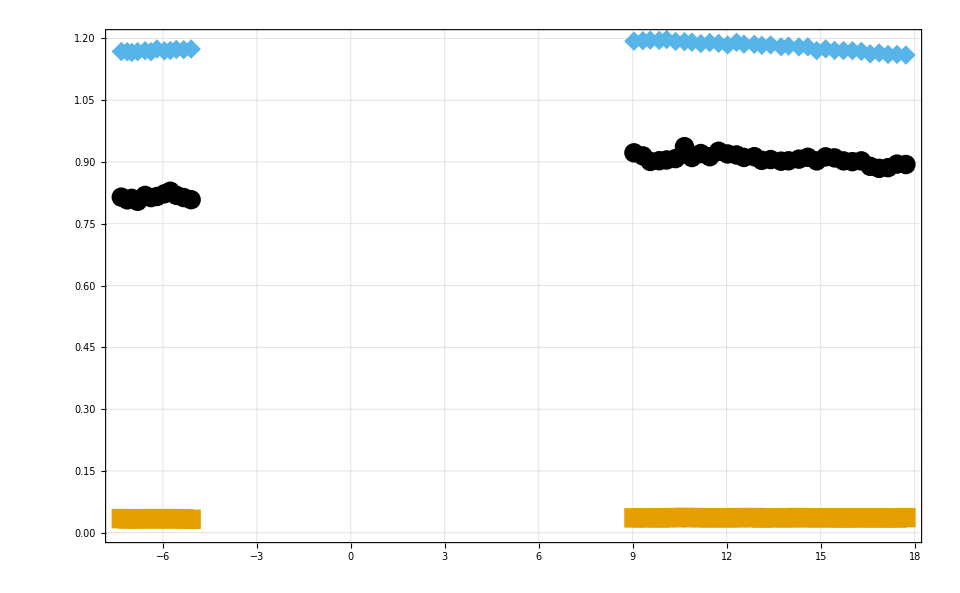

```mathematica
fileName=files[[3]]
datasetRaw=GetFileDataset[fileName];
headerInfo=GetFileHeaderInfo[fileName];
datasetZeroLineRemoved=datasetRaw[Select[#WAV>793&]];
dataset=datasetZeroLineRemoved[All,<|#,"DETUNING"->c/100/(#WAV)-ν0*1*^-9|>&] ;
wingUpper=dataset[Select[#["DETUNING"]> 9&]];
wingLower=dataset[Select[#["DETUNING"]< -5&]];
wingsDataset=Join[wingUpper,wingLower][SortBy["DETUNING"]];
plotList={Normal[dataset[All,{"DETUNING","VERT"}][Values]],Normal[dataset[All,{"DETUNING","HORIZ"}][Values]],Normal[dataset[All,{"DETUNING","REF"}][Values]]};
ListPlot[plotList[[{3}]],Joined->True,PlotRange->Full];
wingsPlotList={Normal[wingsDataset[All,{"DETUNING","VERT"}][Values]],Normal[wingsDataset[All,{"DETUNING","HORIZ"}][Values]],Normal[wingsDataset[All,{"DETUNING","REF"}][Values]]}
ListPlot[wingsPlotList]
```

```mathematica
nlmFit["BestFit"]
```

0.877049+0.00746337 x-0.000376393 x^2

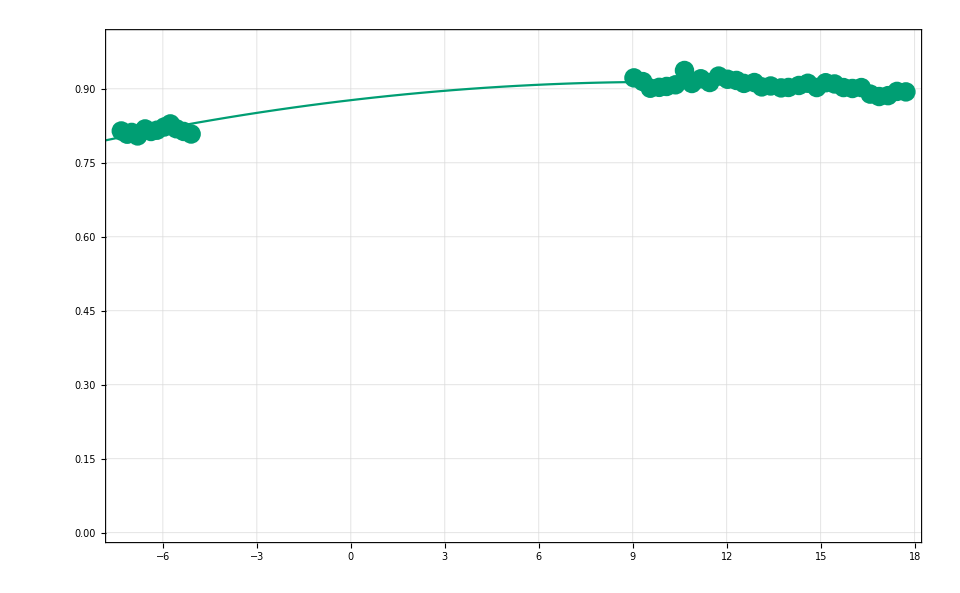

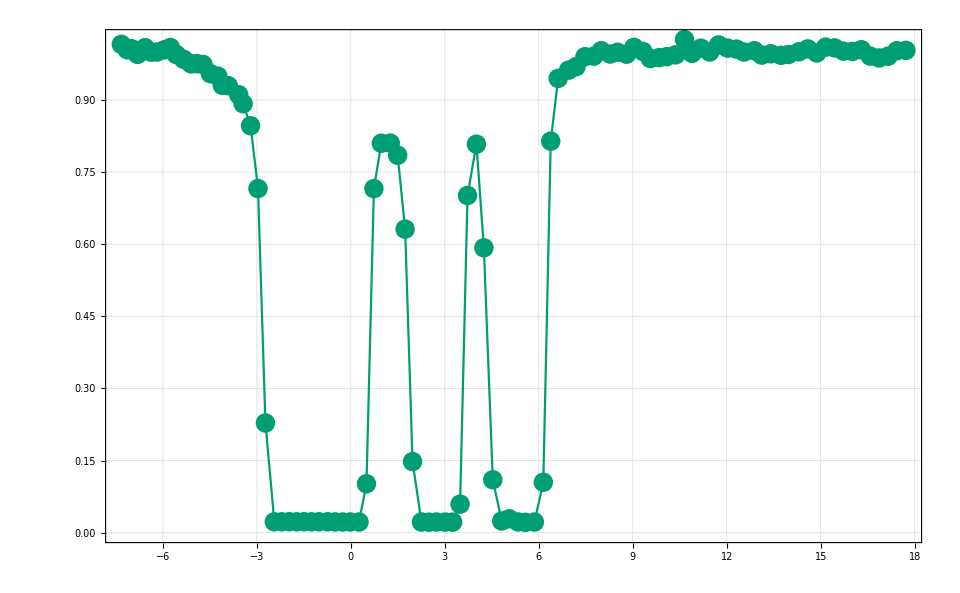

```mathematica
nlmFit=NonlinearModelFit[wingsPlotList[[1]],a x^2+b x+d,{a,b,d},x];
Show[Reverse[{Plot[nlmFit[x],{x,-10,15}],ListPlot[wingsPlotList[[1]],PlotRange->{Automatic,{0,1}}]}]]
newList={};
For[i=1,i≤Length[plotList[[1]]],i++,
AppendTo[newList,{plotList[[1]][[i]][[1]],plotList[[1]][[i]][[2]]/nlmFit[plotList[[1]][[i]][[1]]]}];
];
ListPlot[newList,Joined->True]
```

```mathematica
NormalizeProfileWithWings[dataset_,abscissaColumnName_,ordinateColumnName_,lowCutoff_:-6,highCutoff_:9]:=Module[{detuningColumnName,datasetZeroLineRemoved,wingUpper,wingLower,wingsDataset,nlmFit,a,b,d,x,newList,i},
wingUpper=dataset[Select[#[abscissaColumnName]> highCutoff&]];
wingLower=dataset[Select[#[abscissaColumnName]< lowCutoff&]];
wingsDataset=Join[wingUpper,wingLower][SortBy[abscissaColumnName]];


nlmFit=NonlinearModelFit[Normal[wingsDataset[All,{abscissaColumnName,ordinateColumnName}][All,Values]],a x^2+b x+d,{a,b,d},x];
(*Show[Reverse[{Plot[nlmFit[x],{x,-10,15}],ListPlot[wingsOrderedPairs,PlotRange->{Automatic,{0,1}}]}]];*)
dataset[All,<|#,ordinateColumnName<>"NORMWW"->#[ordinateColumnName]/nlmFit[#[abscissaColumnName]]|>&]
];
```

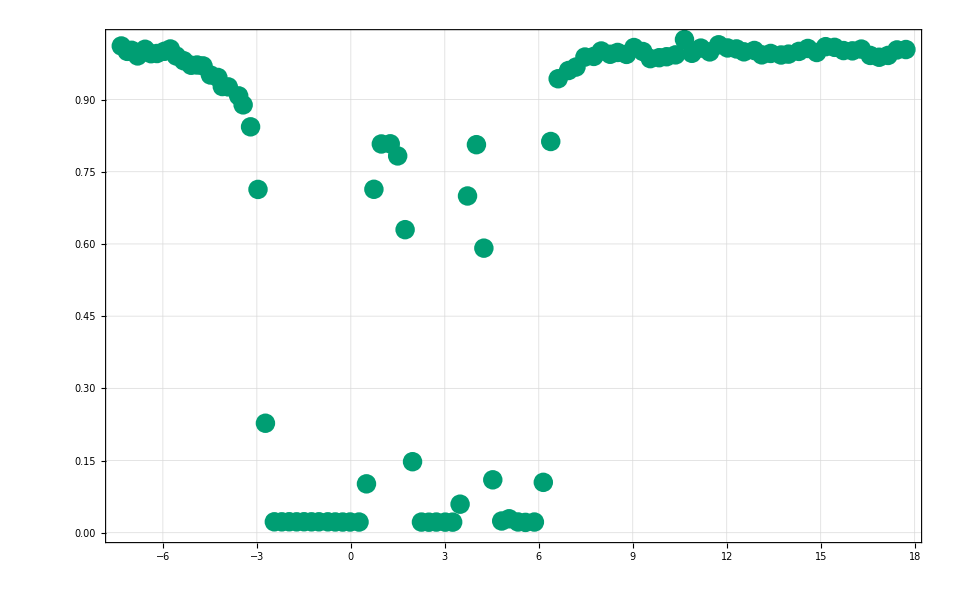

```mathematica
ListPlot[NormalizeProfileWithWings[dataset,"DETUNING","VERT"][All,{"DETUNING","VERTNORMWW"}]]
```

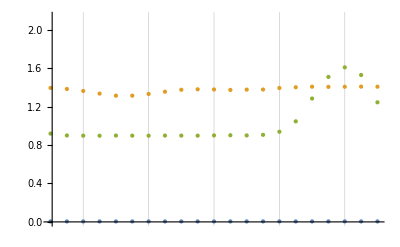

```mathematica
low=250;
QuickPlotRbProfileWithRange[datasetRaw,{low,low+100}]
```

```mathematica
{firstTrans,firstTransLetter,lastTransLetter}={270,"D","A"};
(*maxDataset=SlopeInterceptProfileConversion[maxDatasetRaw,-.0272,-1.407];*)
datasetDet=ConvertAoutProfileToDetuning[datasetRaw,firstTrans,firstTransLetter,lastTransLetter];
```

FittedModel[11.3453-0.0247345 x]

## Profiles with transitions Marked

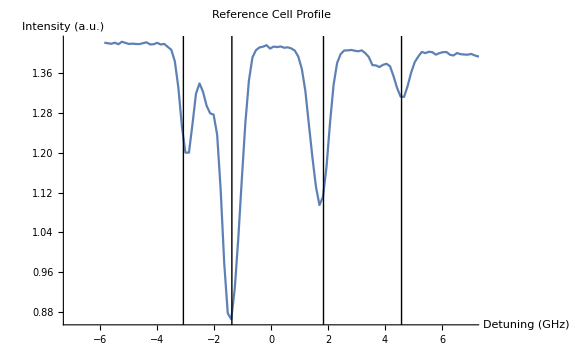

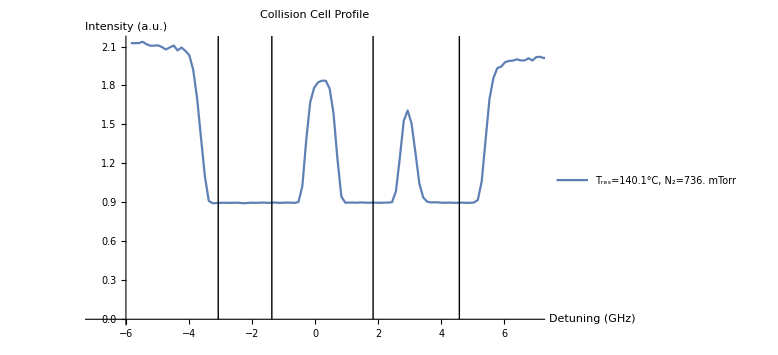

```mathematica
data ={headerInfo,datasetDet};
torrTomTorrConv=1000;

label="T_res="<>
ToString[headerInfo["#CurrTemp(Res):"]]<>
"°C,\nN_2="<>
ToString[headerInfo["#CVGauge(N2)(Torr):"]*torrTomTorrConv]<>
" mTorr";

transitionLines=Line[{{{transGHz[[1]],0},{transGHz[[1]],10}},{{transGHz[[2]],0},{transGHz[[2]],10}},{{transGHz[[3]],0},{transGHz[[3]],10}},{{transGHz[[4]],0},{transGHz[[4]],10}}}];

ListPlot[GetOrderedPairs[data[[2]],"REF"],
PlotRange->{{-7,7},All},
ImageSize->Large,
PlotLabel->"Reference Cell Profile",
AxesLabel->{"Detuning (GHz)","Intensity (a.u.)"},
AxesOrigin->{-6,0},
Joined->True,
LabelStyle->labelSize,
Epilog->Style[transitionLines,Dotted]]

plot=ListPlot[{Legended[GetOrderedPairs[data[[2]],"PMP"],label]}
,PlotRange->{{-7,7},Full},
PlotLabel-> "Collision Cell Profile",
AxesLabel->{"Detuning (GHz)",
"Intensity (a.u.)"},
AxesOrigin->{-6,0},
Joined->True,
LabelStyle->labelSize,
Epilog->Style[transitionLines,Dotted]]
```

```mathematica
Rasterize[plot]
```

-Graphics-

Part::pkspec1: The expression Values cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

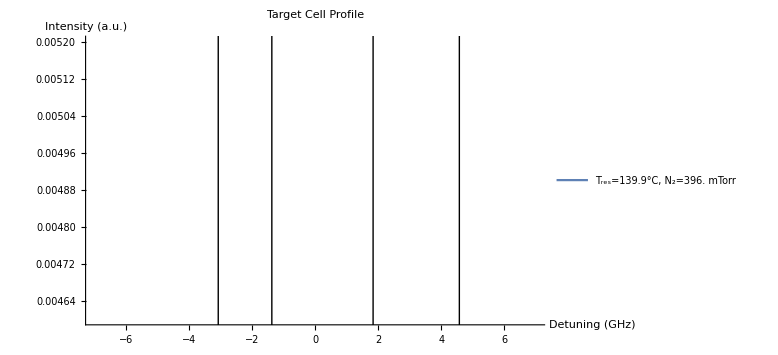

```mathematica
ListPlot[{Legended[GetOrderedPairs[data,"PRB"],label]}
,PlotRange->{{-7,7},All},
PlotLabel-> "Target Cell Profile",
AxesLabel->{"Detuning (GHz)",
"Intensity (a.u.)"},
AxesOrigin->{-6,0},
Joined->True,
LabelStyle->labelSize,
Epilog->Style[transitionLines,Dotted]]
```

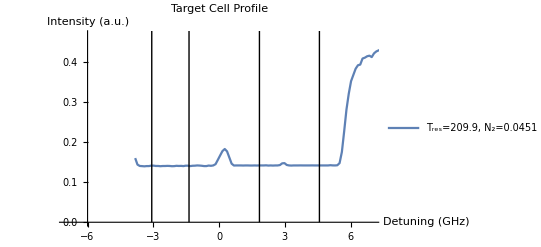

```mathematica
plot151725
```

Dataset[<>]

{{9.40851,0.966983},{9.28294,0.963855},{9.15737,0.957506},{9.0318,0.962024},{8.90622,0.971182},{8.78065,0.961614},{8.65508,0.960562},{8.52951,0.957765},{8.40394,0.948638},{8.27837,0.954409},{8.1528,0.967435},{8.02723,0.965074},{7.90166,0.968932},{7.77609,0.962918},{7.65052,0.962849},{7.52495,0.964743},{7.39938,0.972415},{7.27381,0.967603},{7.14824,0.973311},{7.02267,0.96305},{6.8971,0.96053},{6.77153,0.96787},{6.64596,0.967583},{6.52038,0.960106},{6.39481,0.966355},{6.26924,0.967211},{6.14367,0.972205},{6.0181,0.961629},{5.89253,0.972828},{5.76696,0.957465},{5.64139,0.949615},{5.51582,0.915325},{5.39025,0.851612},{5.26468,0.764144},{5.13911,0.683334},{5.01354,0.652141},{4.88797,0.643412},{4.7624,0.642569},{4.63683,0.641889},{4.51126,0.642731},{4.38569,0.64629},{4.26012,0.655173},{4.13455,0.682854},{4.00897,0.702052},{3.8834,0.703646},{3.75783,0.713441},{3.63226,0.734746},{3.50669,0.775648},{3.38112,0.836518},{3.25555,0.893735},{3.12998,0.940137},{3.00441,0.950654},{2.87884,0.939191},{2.75327,0.916338},{2.6277,0.841628},{2.50213,0.727991},{2.37656,0.658314},{2.25099,0.641527},{2.12542,0.642151},{1.99985,0.641418},{1.87428,0.640469},{1.74871,0.639574},{1.62313,0.640848},{1.49756,0.64082},{1.37199,0.640089},{1.24642,0.637949},{1.12085,0.647672},{0.995282,0.70879},{0.869712,0.819659},{0.744141,0.914419},{0.618571,0.958101},{0.493,0.972486},{0.367429,0.976422},{0.241859,0.960441},{0.116288,0.968544},{-0.00928207,0.966257},{-0.134853,0.957154},{-0.260423,0.9381},{-0.385994,0.872972},{-0.511564,0.751187},{-0.637135,0.661659},{-0.762705,0.638814},{-0.888276,0.637003},{-1.01385,0.636382},{-1.13942,0.636193},{-1.26499,0.634978},{-1.39056,0.63668},{-1.51613,0.634654},{-1.6417,0.638085},{-1.76727,0.637842},{-1.89284,0.636897},{-2.01841,0.636276},{-2.14398,0.633874},{-2.26955,0.633038},{-2.39512,0.634954},{-2.52069,0.638328},{-2.64626,0.636304},{-2.77183,0.635198},{-2.8974,0.633985},{-3.02297,0.634228},{-3.14855,0.635928},{-3.27412,0.63822},{-3.39969,0.707803},{-3.52526,0.81721},{-3.65083,0.919259},{-3.7764,0.969268},{-3.90197,0.999379},{-4.02754,1.00259},{-4.15311,0.994978},{-4.27868,1.00191},{-4.40425,0.995641},{-4.52982,1.00149},{-4.65539,1.01004},{-4.78096,0.989071},{-4.90653,0.995622},{-5.0321,1.00083},{-5.15767,1.00301},{-5.28324,0.996105},{-5.40881,1.00071},{-5.53438,1.00312}}

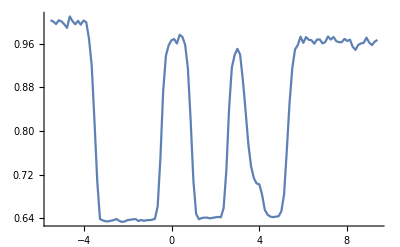

```mathematica
normalizedProfile=NormalizeProfile[datasetDet](*Adds a colum PRBNRMWWING (Probe normalization with WINGS*)
ordPair=GetOrderedPairs[normalizedProfile,"PRBNRMWWING"] (*PRoBeNoRMaliztionWithWINGs*)
ListLinePlot[ordPair]
```

```mathematica
datasetDet
```

Dataset[<>]

## Initialization and Folder Selection

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];

dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns"}];
If[SystemInformation["Kernel","OperatingSystem"]=="Unix",
folder=FileNameJoin[{"/","home","karl",dropBoxOn}]; ,(* Home coputer is Linux, so needs "/" at beginning *)
folder=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"*)
];
SetDirectory[folder];

FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-05-25_LaserProfiling - Shortcut.lnk,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,18-03-01,18-03-02,18-03-03,18-03-06_RubidiumOnWalls,18-03-18_100mTorrBGP,18-03-22_Ei=37eV,18-03-23_pumpScan,18-03-24_higherTemps350mTorr,18-03-25_springBreakDataReview,18-03-27_770mTorr,18-03-28_PumpPowerScan,18-04-09_PumpLaserRazorProfile,18-04-18,18-05-04,18-05-07,18-06-03,2018-06-07,2018-06-15,2018-06-19_CO2_Data,2018-06-21_ProbeWalkData,2018-06-25,dataDump,POL2018-03-18.dat,pumpQWP,README.txt,reallyNiceData,temp,test.png,wavemeterOffsets}

```mathematica
{"15-06-09_USBCounterError","15-07-06mockPolarizationData","16-01-14","16-01-21_Data","16-05-25_PolarizationData","16-07-06_PolarizationData","16-08-04_PolarizationData","16-08-07_HeliumTargetPictures","16-08-09_PolarizationData","16-10-17_polarimeter","16-10-27_DataReport","16-11-03_faradayRotation","16-11-07_faradayRotation","16-11-18_faradayRotation","16-12-09_faradayRotation","17-01-31","17-02-17_plusMinus","17-03-06_PlusMinusWavemeter","17-03-10_non-RbFaradayRotation","17-03-15_AimingFor5e12","17-03-15_wavemeterNoRb","17-03-28","17-03-29_pumpLaserFindingCircular","17-03-30_WavemeterReliability","17-04-04_polarization","17-04-06_polarization","17-04-07_wmReliability","17-04-18","17-04-18_polarization","17-04-22","17-04-25_ProbePolarizationDriftOpenChamber","17-04-30_laserReport","17-05-17_DirtyGunRun","17-05-18_ProbeDrift","17-05-19_BetterLaser","17-05-24_SimplifiedPolarization","17-05-25_LaserProfiling","17-05-25_LaserProfiling - Shortcut.lnk","17-06-02","17-06-06_IntensityOfProbeStudy","17-06-11","17-06-13","17-06-16","17-06-17","17-06-25","17-07-01_nRbVsBufferGasAnalysis","17-07-01_PumpLaserAnalysis","17-07-03_lowerNRb_BGPStudy","17-07-03_ProbeDrift","17-07-03_pumpBroadening","17-07-06_lotsOfProbeMeasurements","17-07-06_MagneticField","17-07-06_probePower","17-07-12_polVsPumpPower","17-08-01_rgaInitialScans","17-08-03_redoingSystemDiagnostic","17-08-06_probeDrift","17-08-18_furtherPolarizationStudy","17-08-19_furtherPolarizationStudy2","17-08-22_furtherPolarizationStudyFoundLeak","17-08-29_BvsProbePower_probeDetuneVsMagnetRot","17-09-05_Polarizations_100mTBGP","17-09-20","17-10-03_ElectronGun","17-10-16_ElectronGun","17-10-24_UnpolarizedPolarization","17-10-26_24And30eVRuns","17-10-28_24and30eVRedux","17-11-04_MoreUnpolarizedRuns","17-11-06_UnpolarizedRuns2","17-11-15_BalancedPhotoDetector","17-11-18_SystemDiagnosis","17-12-18_SystemDiagnosis","17-12-20_PolarizingElectrons","18-01-03_PolarizingElectrons","18-01-04_PolarizingElectrons","18-01-10_ChamberWarming","18-01-11_SystemDiagnostics","18-01-12_recreatingPolFigure","18-01-13_recreatingPolFigureIncreasedT","18-01-16_morePolarization","18-01-20_electronPolarization","18-01-25_excitationFunctions","18-01-28_bufferGasPressureVsCounts","18-01-28_exFnCurrentNormalized.png","18-01-28_exFnMolyCounts.png","18-01-28_exFnRawCounts.png","18-01-28_exFnSignalCounts.png","18-01-28_hayesReproduction","18-02-12_polarizedElectrons","18-02-13","18-02-24_DataFrom18-02-13AllElectronEi100","18-02-27","18-03-01","18-03-02","18-03-03","18-03-06_RubidiumOnWalls","18-03-18_100mTorrBGP","18-03-22_Ei=37eV","18-03-23_pumpScan","18-03-24_higherTemps350mTorr","18-03-25_springBreakDataReview","18-03-27_770mTorr","18-03-28_PumpPowerScan","18-04-09_PumpLaserRazorProfile","18-04-18","18-05-04","18-05-07","18-06-03","2018-06-07","2018-06-15","2018-06-19_CO2_Data","2018-06-21_ProbeWalkData","2018-06-25","dataDump","POL2018-03-18.dat","pumpQWP","README.txt","reallyNiceData","temp","test.png","wavemeterOffsets"}
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-05-25_LaserProfiling - Shortcut.lnk,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,18-03-01,18-03-02,18-03-03,18-03-06_RubidiumOnWalls,18-03-18_100mTorrBGP,18-03-22_Ei=37eV,18-03-23_pumpScan,18-03-24_higherTemps350mTorr,18-03-25_springBreakDataReview,18-03-27_770mTorr,18-03-28_PumpPowerScan,18-04-09_PumpLaserRazorProfile,18-04-18,18-05-04,18-05-07,18-06-03,2018-06-07,2018-06-15,2018-06-19_CO2_Data,2018-06-21_ProbeWalkData,2018-06-25,dataDump,POL2018-03-18.dat,pumpQWP,README.txt,reallyNiceData,temp,test.png,wavemeterOffsets}

```mathematica
SetDirectory[FileNameJoin[{folder,"2018-06-25","data"}]];
absorptionFileNames=FileNames[StringExpression["Rb",__,"_",__,DigitCharacter,".dat"]]
```

{RbAbs2018-06-25_143546.dat,RbAbs2018-06-25_160329.dat,RbAbs2018-06-25_162855.dat,RbAbs2018-06-25_163537.dat,RbAbs2018-06-25_165701.dat,RbAbs2018-06-25_170301.dat,RbAbs2018-06-25_172001.dat,RbAbs2018-06-25_174001.dat,RbAbs2018-06-25_174802.dat,RbAbs2018-06-25_175401.dat,RbAbs2018-06-25_180001.dat,RbAbs2018-06-25_180601.dat,RbAbs2018-06-25_181201.dat,RbAbs2018-06-25_181802.dat}

## Data Cleaning

```mathematica
ApproximateFrequency[data_,columnMissing_,columnReference_,missingEntry_]:=Module[{j,adjacentSpots,referenceSpacing,validEntries,fit}(*These are your local variables that aren't stored beyond the scope of the module.*),
(*Selects the data that is certainly an appropriate measure of wavelength *)
adjacentSpots={};
validEntries=data[All,{columnReference,columnMissing}][Select[#[columnMissing]>793&]];
(*The "reference column" is the column that is monotonically increasing, we need to know what the size of spaces between these values is *)
referenceSpacing=2;
j=1;
(* This "While" loop accumulates adjacent data points used to approximate the missing frequency, we only want the closest datapoints. *)
While[And[Length[adjacentSpots]<3,Abs[j*referenceSpacing]<117](* We want a few data points to approximate where our point lies, keep going until we have at least 3*),
adjacentSpots=validEntries[Select[Abs[#[columnReference]-missingEntry]≤referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots[Values]],x,x];
fit[missingEntry] (* Last line is the "return" statement, all other lines need a semi-colon*)
];

(* This is called on a dataset to fill in all of the missing frequency gaps.*)
FillInMissedFrequencies[rawdata_,columnMissing_,columnReference_]:=Module[{referenceSpacing,missingEntries,validEntries,adjacentSpots,estimatedFrequency,linearModel,dataCopy,dataReturn,position,approxValue,data2,k},
dataCopy=Dataset[rawdata];
dataReturn=Normal[dataCopy];
missingEntries=dataCopy[Select[#[columnMissing]<793&]];
missingEntries=Flatten[Normal[missingEntries[All,{columnReference}][Values]]];
For[k=1,k<=Length[missingEntries],k++,
approxValue=ApproximateFrequency[dataCopy,columnMissing,columnReference,missingEntries[[k]]];
(* Find the index of the missing value in the list *)
position=Position[dataCopy,missingEntries[[k]]][[1,1]];
(* Use the index to insert the approximate value in the data  *)
dataReturn[[position,columnMissing]]=approxValue;
];
dataReturn
];

CleanDataset[dataset_,missingColumn_,referenceColumn_]:=Module[{d,d2,i},
d=FillInMissedFrequencies[Normal[dataset[All,{referenceColumn,missingColumn}]],missingColumn,referenceColumn];
d2=Normal[dataset];
For[i=1,i≤Length[d2],i++,
AppendTo[d2[[i]],"WAV"->d[[i]]["WAV"]]
];
Dataset[d2]
];
```

```mathematica
headerInfo["CurrTemp(Res)"]
```

154.5

## Plot Options Setting

```mathematica
colorBlindPallete={RGBColor[230/255,159/255,0],RGBColor[86/255,180/255,233/255],RGBColor[0/255,158/255,115/255],RGBColor[240/255,228/255,66/255],RGBColor[0/255,114/255,178/255],RGBColor[213/255,94/255,0/255],RGBColor[204/255,121/255,167/255],RGBColor[0/255,0/255,0/255]};
SetOptions[Plot,BaseStyle->{FontSize->24},Frame->True,ImageSize->Large,LabelStyle->27,GridLines->Automatic];
SetOptions[ListPlot,BaseStyle->{FontSize->24},Frame-> True,ImageSize->Large,LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];
SetOptions[ListLogPlot,BaseStyle->{FontSize->24},ImageSize->Large,LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];
SetOptions[BarChart,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic];
```

## Import File

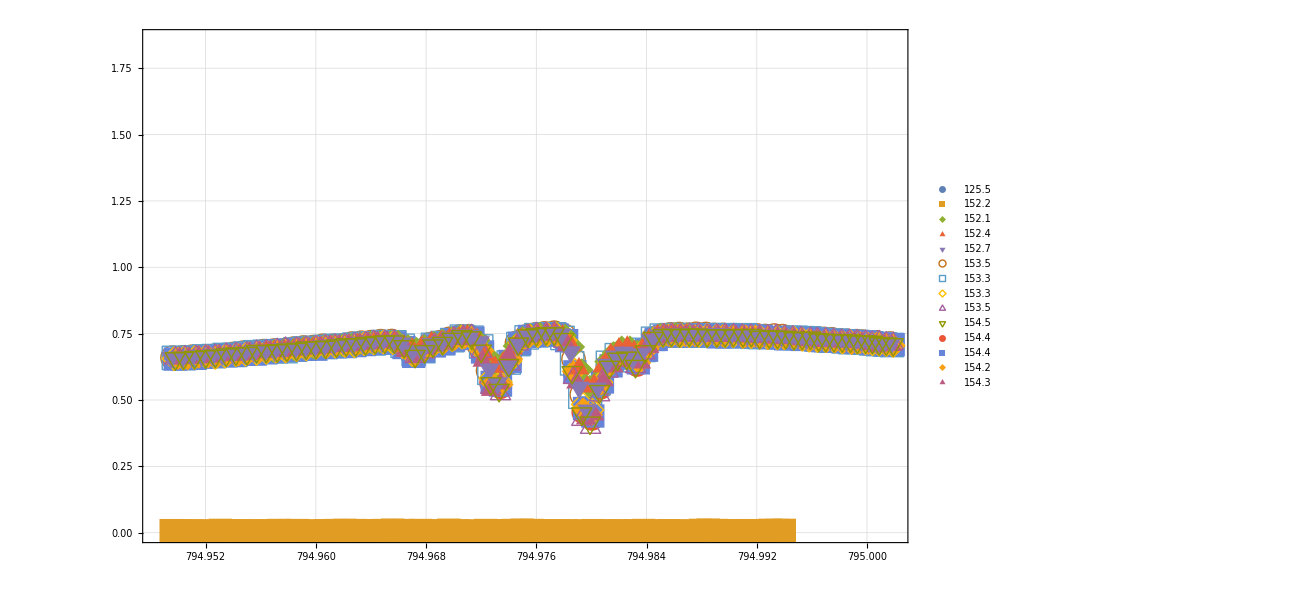

```mathematica
ordPairsList={};
legendList={};
For[i=1,i≤Length[absorptionFileNames],i++,
importedFile=ImportFile[absorptionFileNames[[i]]];
dataset=importedFile[[2]];
headerInfo=importedFile[[1]];
dataset=CleanDataset[dataset,"WAV","VOLT"];
ordPairProbeDataset=Normal[dataset[All,{"WAV","PRB"}][Values]];
AppendTo[ordPairsList,ordPairProbeDataset];
AppendTo[legendList,headerInfo["CurrTemp(Res)"]]
]
ListPlot[ordPairsList,PlotRange->{0,Automatic},PlotLegends->legendList,PlotMarkers->{Automatic,24}]
```

```mathematica
ordPairsList
```

{{{794.994,9.9841},{794.993,9.9841},{794.993,9.9847},{794.992,9.9835},{794.992,9.9841},{794.992,9.9844},{794.991,9.9844},{794.991,9.9844},{794.99,9.9838},{794.99,9.9838},{794.989,9.9844},{794.989,9.9838},{794.988,9.9841},{794.988,9.9841},{794.988,9.9844},{794.987,9.9841},{794.987,9.9841},{794.986,9.9844},{794.986,9.9841},{794.985,9.9841},{794.985,9.9844},{794.984,9.9835},{794.984,9.9841},{794.983,9.9844},{794.983,9.9835},{794.982,9.9838},{794.982,9.9835},{794.981,9.9841},{794.981,9.9841},{794.98,9.9841},{794.98,9.9838},{794.98,9.9841},{794.979,9.9847},{794.978,9.9838},{794.978,9.9841},{794.977,9.9841},{794.977,9.9838},{794.976,9.9838},{794.976,9.9847},{794.975,9.9847},{794.975,9.9841},{794.974,9.9841},{794.974,9.9841},{794.973,9.9847},{794.973,9.9838},{794.972,9.9838},{794.972,9.9841},{794.971,9.9838},{794.971,9.9838},{794.97,9.9838},{794.969,9.9841},{794.969,9.9841},{794.968,9.9838},{794.968,9.9844},{794.967,9.9832},{794.967,9.9844},{794.966,9.9826},{794.966,9.9838},{794.965,9.9844},{794.964,9.9841},{794.964,9.9838},{794.963,9.9838},{794.963,9.9835},{794.962,9.9841},{794.962,9.9844},{794.961,9.9838},{794.96,9.9841},{794.96,9.9838},{794.959,9.9838},{794.959,9.9841},{794.958,9.9841},{794.958,9.9835},{794.957,9.9835},{794.957,9.9838},{794.956,9.9832},{794.955,9.9838},{794.955,9.9841},{794.954,9.9841},{794.954,9.9835},{794.953,9.9835},{794.953,9.9835},{794.952,9.9844},{794.951,9.9841},{794.951,9.985},{794.95,9.9841},{794.95,9.9835},{794.949,9.9838},{794.949,9.9844}},{{794.994,0.0089},{794.994,0.0085},{794.993,0.0092},{794.993,0.007},{794.992,0.0073},{794.991,0.0079},{794.991,0.0076},{794.99,0.0073},{794.99,0.0046},{794.989,0.0085},{794.988,0.0095},{794.988,0.0089},{794.987,0.0058},{794.987,0.0058},{794.986,0.0064},{794.986,0.0076},{794.985,0.0064},{794.984,0.0061},{794.984,0.0085},{794.983,0.007},{794.983,0.0061},{794.982,0.0073},{794.981,0.0067},{794.981,0.0067},{794.98,0.0079},{794.98,0.0064},{794.979,0.0061},{794.978,0.007},{794.978,0.0073},{794.977,0.0073},{794.976,0.0073},{794.976,0.0085},{794.975,0.0095},{794.974,0.0085},{794.974,0.007},{794.973,0.0076},{794.972,0.0085},{794.972,0.0064},{794.971,0.0058},{794.97,0.0073},{794.97,0.0095},{794.969,0.007},{794.968,0.007},{794.968,0.0085},{794.967,0.0064},{794.966,0.0082},{794.966,0.0095},{794.965,0.0082},{794.964,0.0079},{794.964,0.0073},{794.963,0.0082},{794.962,0.0089},{794.961,0.0082},{794.961,0.0073},{794.96,0.0073},{794.959,0.0043},{794.959,0.0082},{794.958,0.0079},{794.957,0.0085},{794.957,0.0073},{794.956,0.0067},{794.955,0.0073},{794.955,0.007},{794.954,0.0076},{794.953,0.0089},{794.952,0.0058},{794.952,0.007},{794.951,0.0067},{794.95,0.0076},{794.95,0.0079}},{{794.987,0.7468},{794.987,0.748},{794.986,0.7496},{794.986,0.7453},{794.985,0.7462},{794.984,0.7319},{794.984,0.7019},{794.983,0.6833},{794.983,0.6992},{794.982,0.6992},{794.982,0.6781},{794.981,0.6448},{794.981,0.5743},{794.98,0.5508},{794.979,0.6137},{794.979,0.6998},{794.978,0.7438},{794.977,0.7535},{794.977,0.7465},{794.976,0.7514},{794.976,0.7444},{794.975,0.7346},{794.974,0.7035},{794.974,0.6473},{794.973,0.6253},{794.972,0.669},{794.972,0.723},{794.971,0.7419},{794.971,0.7422},{794.97,0.7337},{794.969,0.7248},{794.969,0.7163},{794.968,0.7041},{794.967,0.694},{794.967,0.7038},{794.966,0.7206},{794.965,0.7197},{794.965,0.7184},{794.964,0.7169},{794.963,0.7123},{794.963,0.7087},{794.962,0.7053},{794.961,0.7038},{794.961,0.7016},{794.96,0.6971},{794.959,0.6968},{794.958,0.691},{794.958,0.6913},{794.957,0.6836},{794.956,0.6839}},{{794.987,0.7465},{794.986,0.7459},{794.986,0.748},{794.985,0.7471},{794.985,0.7429},{794.984,0.7282},{794.984,0.6928},{794.983,0.6833},{794.983,0.7004},{794.982,0.6934},{794.981,0.672},{794.981,0.6256},{794.98,0.5563},{794.98,0.5502},{794.979,0.6186},{794.979,0.7059},{794.978,0.7425},{794.977,0.7523},{794.977,0.7493},{794.976,0.7459},{794.976,0.7429},{794.975,0.73},{794.974,0.6934},{794.974,0.64},{794.973,0.6244},{794.972,0.6699},{794.972,0.7291},{794.971,0.7429},{794.97,0.7349},{794.97,0.7309},{794.969,0.7212},{794.968,0.7175},{794.968,0.7001},{794.967,0.6928},{794.966,0.7044},{794.966,0.7181},{794.965,0.7181},{794.964,0.7181},{794.964,0.7135},{794.963,0.7102},{794.962,0.7084},{794.962,0.7035},{794.961,0.7032},{794.96,0.698},{794.96,0.6964},{794.959,0.6937},{794.958,0.6894},{794.958,0.6882},{794.957,0.6845},{794.956,0.6833}},{{795.002,0.7138},{795.001,0.7166},{795.001,0.7151},{795.,0.72},{795.,0.7227},{794.999,0.7218},{794.999,0.723},{794.998,0.7276},{794.997,0.727},{794.997,0.7297},{794.996,0.7319},{794.996,0.7303},{794.995,0.7334},{794.994,0.7367},{794.994,0.7395},{794.993,0.7425},{794.993,0.7422},{794.992,0.7425},{794.991,0.7435},{794.991,0.7441},{794.99,0.7441},{794.989,0.7487},{794.989,0.7496},{794.988,0.7465},{794.988,0.7471},{794.987,0.748},{794.986,0.7474},{794.986,0.7474},{794.985,0.7441},{794.984,0.7255},{794.984,0.6732},{794.983,0.6561},{794.982,0.679},{794.982,0.6644},{794.981,0.6335},{794.98,0.5432},{794.98,0.461},{794.979,0.5471},{794.979,0.6803},{794.978,0.7477},{794.977,0.7548},{794.977,0.7505},{794.976,0.7517},{794.975,0.7398},{794.975,0.7077},{794.974,0.6259},{794.973,0.5636},{794.973,0.6155},{794.972,0.7184},{794.971,0.7425},{794.971,0.7438},{794.97,0.7334},{794.969,0.7172},{794.968,0.7114},{794.968,0.6842},{794.967,0.6839},{794.966,0.7135},{794.966,0.7236},{794.965,0.7197},{794.964,0.7187},{794.963,0.7154},{794.963,0.7123},{794.962,0.7108},{794.961,0.7068},{794.961,0.7035},{794.96,0.6995},{794.959,0.6958},{794.959,0.6937},{794.958,0.6928},{794.957,0.6864},{794.956,0.6839},{794.956,0.6833},{794.955,0.6781},{794.954,0.6751},{794.953,0.672},{794.953,0.6693},{794.952,0.6665},{794.951,0.6641},{794.95,0.6598},{794.95,0.6595}},{{795.002,0.705},{795.001,0.7084},{795.001,0.7099},{795.,0.7114},{795.,0.7157},{794.999,0.7175},{794.999,0.7197},{794.998,0.7187},{794.998,0.7227},{794.997,0.7236},{794.996,0.7239},{794.996,0.7248},{794.995,0.7285},{794.995,0.7328},{794.994,0.7337},{794.994,0.7343},{794.993,0.734},{794.992,0.7389},{794.992,0.7386},{794.991,0.7389},{794.99,0.7413},{794.99,0.7404},{794.989,0.7429},{794.988,0.7435},{794.988,0.7435},{794.987,0.7429},{794.987,0.7432},{794.986,0.7432},{794.985,0.7429},{794.985,0.7331},{794.984,0.6928},{794.983,0.651},{794.983,0.6644},{794.982,0.665},{794.981,0.6375},{794.981,0.5664},{794.98,0.4626},{794.979,0.4833},{794.979,0.6119},{794.978,0.7248},{794.978,0.7462},{794.977,0.7468},{794.976,0.7422},{794.976,0.7419},{794.975,0.7169},{794.974,0.647},{794.973,0.5679},{794.973,0.5823},{794.972,0.6882},{794.971,0.7337},{794.971,0.7364},{794.97,0.7267},{794.969,0.7142},{794.969,0.7041},{794.968,0.6845},{794.967,0.6708},{794.966,0.7004},{794.966,0.7157},{794.965,0.7178},{794.964,0.7148},{794.964,0.712},{794.963,0.7038},{794.962,0.7053},{794.961,0.7022},{794.961,0.7013},{794.96,0.6977},{794.959,0.6922},{794.959,0.6891},{794.958,0.6845},{794.957,0.6839},{794.956,0.6793},{794.956,0.6754},{794.955,0.672},{794.954,0.6705},{794.953,0.6653},{794.953,0.6601},{794.952,0.6641},{794.951,0.6598},{794.95,0.6574},{794.95,0.6558}},{{795.002,0.7123},{795.001,0.7138},{795.001,0.7184},{795.,0.7151},{795.,0.719},{794.999,0.7212},{794.999,0.7227},{794.998,0.723},{794.998,0.7267},{794.997,0.7297},{794.996,0.73},{794.996,0.7313},{794.995,0.7337},{794.995,0.7358},{794.994,0.7386},{794.993,0.7416},{794.993,0.7404},{794.992,0.7407},{794.992,0.7429},{794.991,0.7429},{794.99,0.7447},{794.99,0.745},{794.989,0.7435},{794.988,0.7429},{794.988,0.7474},{794.987,0.7459},{794.986,0.7435},{794.986,0.7444},{794.985,0.7441},{794.985,0.7316},{794.984,0.6772},{794.983,0.6253},{794.983,0.6485},{794.982,0.651},{794.981,0.6082},{794.981,0.5191},{794.98,0.3966},{794.979,0.4265},{794.979,0.5844},{794.978,0.7206},{794.977,0.7523},{794.977,0.7496},{794.976,0.7484},{794.975,0.7416},{794.975,0.7105},{794.974,0.6357},{794.973,0.523},{794.973,0.5471},{794.972,0.6827},{794.971,0.7416},{794.971,0.7392},{794.97,0.7316},{794.969,0.7142},{794.969,0.7071},{794.968,0.6809},{794.967,0.6632},{794.966,0.6992},{794.966,0.7209},{794.965,0.72},{794.964,0.719},{794.964,0.7148},{794.963,0.7099},{794.962,0.7074},{794.961,0.705},{794.961,0.7026},{794.96,0.6995},{794.959,0.6968},{794.959,0.6937},{794.958,0.6937},{794.957,0.6888},{794.956,0.6842},{794.956,0.6824},{794.955,0.6754},{794.954,0.6729},{794.954,0.6714},{794.953,0.6665},{794.952,0.6647},{794.951,0.6622},{794.951,0.6616},{794.95,0.658}},{{795.002,0.709},{795.001,0.7117},{795.001,0.7126},{795.,0.7181},{795.,0.719},{794.999,0.7187},{794.999,0.723},{794.998,0.7236},{794.998,0.7245},{794.997,0.7251},{794.997,0.7273},{794.996,0.7337},{794.995,0.7328},{794.995,0.7319},{794.994,0.7364},{794.994,0.7371},{794.993,0.7386},{794.992,0.7364},{794.992,0.7438},{794.991,0.7429},{794.99,0.7435},{794.99,0.7425},{794.989,0.7429},{794.988,0.7425},{794.988,0.745},{794.987,0.745},{794.986,0.7429},{794.986,0.7444},{794.985,0.7429},{794.985,0.7325},{794.984,0.6824},{794.983,0.6271},{794.983,0.6583},{794.982,0.6543},{794.981,0.6238},{794.981,0.5325},{794.98,0.4137},{794.979,0.4482},{794.979,0.6039},{794.978,0.7285},{794.977,0.7499},{794.977,0.7502},{794.976,0.7471},{794.975,0.7425},{794.975,0.7114},{794.974,0.6308},{794.973,0.5368},{794.973,0.5618},{794.972,0.6845},{794.971,0.7346},{794.971,0.7395},{794.97,0.7291},{794.969,0.7138},{794.969,0.7041},{794.968,0.6827},{794.967,0.665},{794.966,0.7013},{794.966,0.7193},{794.965,0.7193},{794.964,0.7169},{794.964,0.7132},{794.963,0.7084},{794.962,0.7087},{794.962,0.7041},{794.961,0.6995},{794.96,0.698},{794.959,0.6964},{794.959,0.6913},{794.958,0.6888},{794.957,0.6861},{794.956,0.6836},{794.956,0.6833},{794.955,0.676},{794.954,0.6742},{794.954,0.6705},{794.953,0.6656},{794.952,0.6632},{794.951,0.6604},{794.95,0.658},{794.95,0.6558}}}